# Currency Areas and Voluntary Transfers Picard Worrall Updated 11-08-2020 | This Mathematica notebook contains the simulation of the costs and benefits of currency areas compared to flexible exchange rates.

Here are some definitions used in the paper. The letter  z defines the exogenous shock (z in (0,1)). The letter a defines the inverse productivity. The letters G and B stand for good and bad shock. M0 is the normalized money supply. V is the utility for aggregate consumption. The parameters σ, μ, γ, and θ are as defined in the paper. The parameter ψ is the Frisch elasticity measure, which is set equal to 1 in the paper.

```mathematica
aG=z;aB=z;A=(1+z^(1-σ))^(1/(1-σ));
bB=2/(1+z^(1-σ));bG=2 z^(1-σ)/ (1+z^(1-σ)) ;
M0=(1-μ)/μ;
V[x_]=x^(1-γ)/(1-γ);
ξ=μ^μ(1-μ)^(1-μ) ;
κ0=ξ^(γ-1)μ^-γ θ/(θ-1) ;
```

We set some benchmark values for the constants. We may use them or not.  If you evaluate the notebook without changing those variables, then all results are computed for those values.

```mathematica
{z0,μ0,θ0,σ0,γ0,ψ0}={.9,.99,5,2,4, 1};
```

Here are some variable to calibrate the display of graphs. The parameter z is displayed from zmin to 1.

```mathematica
zmin=.8;
```

# Currency Area

We set the values of price indices P, labor supply L, consumption X, utility U and wage W under currency area.
The letter c denotes currency area.

## Currency Area in general

We set the price indices P, labor supply L, consumption X, utility U for any value of shock z, and wage W. 
Shock z and transfer TB are exogenous. We set the value of wage W as a function of shock z and transfer TB.

```mathematica
PGc[W_]=W A ;PBc[W_]=W A ; 
LGc[z_,W_]=bG 1/W;LBc[z_,W_]=bB 1/W;  
XGc[z_,TB_,W_]=ξ(bG-TB+M0)/PGc[W]; XBc[z_,TB_,W_]=ξ(bB+TB+M0)/PBc[W];

UGc[z_,TB_,W_]=V[XGc[z,TB,W]]-(LGc[z,W])^(1+ψ)/(1+ψ); UBc[z_,TB_,W_]=V[XBc[z,TB,W]]-(LBc[z,W])^(1+ψ)/(1+ψ);

EUc[z_,TB_,W_]=1/2 UGc[z,TB,W]+1/2 UBc[z,TB,W];
Wc[z_,TB_]=(κ0((1/2 bG^(1+ψ)+1/2 bB^(1+ψ))/(1/2(μ(bG-TB)+(1-μ))^-γ bG A^(γ-1)+1/2(μ(bB+TB)+(1-μ))^-γ bB A^(γ-1))))^(1/(γ+ψ)); (* preset wage *)

Wc0[z_]=Wc[z,0];(* wage at zero transfer*)
EUc0[z_]=EUc[z,0,Wc0[z]];
```

## Currency Area and Consumption Sharing

We set the values of price indices P, labor supply L, consumption X, utility U and wage W under consumption equalizing.
In this case the transfer TB is set so that consumption is equalized across countries.
Shock z is exogenous.
The letter “o” denotes the “optimum”, that is full consumption sharing.

```mathematica
TBco[z_]=1/2(bG-bB); (* consumption equalizing transfer *)
Wco[z_]=Wc[z,TBco[z]]; 
UGco[z_]=V[XGc[z,TBco[z],Wco[z]]]-(LGc[Wco[z]])^(1+ψ)/(1+ψ); UBco[z_]=V[XBc[z,TBco[z],Wco[z]]]-(LBc[Wco[z]])^(1+ψ)/(1+ψ);
EUco[z_]=1/2 UGco[z]+1/2 UBco[z];
```

# Flexible Exchange Rate

We set the values of price indices P, labor supply L, consumption X, utility U and wage W under flexible exchange rate system.
The letter f denotes the flexible exchange rate system.

## Flexible Exchange Rate in General

We set the price indices P, labor supply L, consumption X, utility U for any value of shock z, and wage W under flexible exchange rate system.  
Here the price index P=ABW where B depends on the exchange rate.
Shock z and transfer TB are exogenous.
We set the value of wage W as a function of shock z and transfer TB. 

Note Home transfer in bad shock is TB>0.
Exchange rate is ϵ=ϵG = ϵRootG[TB] is computed in the good domestic shock!
So,  T_G^*=-T_B/ϵ_B⟺T_G^*=-T_B*ϵ_G. So we must replace TG by -T_B*ϵ.

```mathematica
LGf[z_,ϵ_,TB_,W_]=1/W(1+(TB* ϵ));LBf[z_,ϵ_,TB_,W_]=1/W(1-TB);
BG[z_,ϵ_]=(1/2 bG+1/2 ϵ^(1-σ)bB)^(1/(1-σ));BB[z_,ϵ_]=(1/2 bB+1/2 ϵ^(σ-1)bG)^(1/(1-σ));
PGf[z_,ϵ_,W_]=A BG[z,ϵ] W;  
PBf[z_,ϵ_,W_]=A BB[z,ϵ] W;

XGf[z_,ϵ_,W_]=(ξ/μ) (1/PGf[z,ϵ,W]);XBf[z_,ϵ_,W_]=(ξ/μ) (1/PBf[z,ϵ,W]);

UGf[z_,ϵ_,TB_,W_]=V[XGf[z,ϵ,W]]-(LGf[z,ϵ,TB,W])^(1+ψ)/(1+ψ);
UBf[z_,ϵ_,TB_,W_]=V[XBf[z,ϵ,W]]-(LBf[z,ϵ,TB,W])^(1+ψ)/(1+ψ);
EUf[z_,ϵ_,TB_,W_]=1/2 UGf[z,ϵ,TB,W]+1/2 UBf[z,ϵ,TB,W];
Wf[z_,ϵ_,TB_]=(κ0 (1/2(1+TB*ϵ)^(1+ψ)+1/2(1-TB)^(1+ψ))/(A^(γ-1)(1/2(1+TB*ϵ)(BG[z,ϵ])^(γ-1)+1/2(1-TB)(BB[z,ϵ])^(γ-1))))^(1/(γ+ψ));  (* the preset wage *)
```

We make two definitions of the exchange rate. One as a function of the transfer in good state and the other as function of transfer in bad state (this is the one used in the paper...).

```mathematica
ϵ0[z_,σ_]=(bG/bB)^(-1/σ); (* exchange rate at zero transfers*)

(* implicit equation for exchange rate Home in good state for a TG<0 *)
ExchEQGTG[eG_,z_,TG_,σ_]=eG-(bG/bB)^(-1/σ) ((1-TG)/(1+TG/eG))^(1/σ); 
ϵRootGTG[z_,TG_,σ_]:= (* exchange rate in Home in Good state when transfer is TG <0 :  a root of the previous implicit equation*)
Module[{},
If[TG==0,
Return[ϵ0[z,σ]],
eG/.FindRoot[ExchEQGTG[eG,z,TG,σ],{eG,ϵ0[z,σ]}]
]
];

(* implicit equation for exchange rate Home in good state for a transfer TB=-TG/ϵ >0 from foreign in bad state *)
ExchEQGTB[eG_,z_,TB_,σ_]=eG-(bG/bB)^(-1/σ) ((1+ eG TB)/(1-TB))^(1/σ); 

ϵRootGTB[z_,TB_,σ_]:= (* exchange rate in Home in Good state when transferin bad state is TB= -TG/ϵ >0 :  a root of the previous implicit equation*)
Module[{},
If[TB==0,
Return[ϵ0[z,σ]],
eG/.FindRoot[ExchEQGTB[eG,z,TB,σ],{eG,ϵ0[z,σ]}]
]
]
(*attention ϵRootGTB function may not find the appropriate root for large TB,close to one*)
```

# Sustainable Transfer Systems

We plot the utility under flexible exchange rates with no transfers and the utility under currency area with full consumption sharing for a range of shocks z and elasticity of substitution σ and for two sets of elasticity of labor supply Ψ and risk aversion γ. 
Basically we compute the locus where EUc is equal to EUf.

```mathematica
ThisPlotPoints=50;
zmin=.8;
rule2={μ->μ0,θ ->θ0,ψ->1};
ThisFrameLabel={
"z",
"σ",
"EUc-EUf",
ThisString=("θ="<>ToString[θ0]<>", μ="<>ToString[μ0])};
TPlot1=Show[
Table[
ContourPlot[
EUc[z,TBco[z],Wc[z,TBco[z]]]-EUf[z,e,0,W]//.{e->ϵRootGTB[z,0,σ],W->Wf[z,e,0]}/. rule2 //Evaluate,{z,zmin,.999},{σ,1.01,3.25},Contours->{0},ContourShading->False, PlotPoints->Floor[ThisPlotPoints],
ContourStyle->GrayLevel[0.1]],
{γ,1.0001,6.0001,1}]
];

TPlot=Show[TPlot1,Frame->True];
```

## Sustaining consumption sharing

Consumption sharing transfers are sustainable if the value function V_G  is positive when transfers implement consumption sharing.
The value function V_G is denoted by the function VGsc where the letter “s” stands for “sustaining consumption sharing”.
The letter c and f denote currency area and flexible exchange rate system.
The critical discount factors δ are found where VGsc=0 and is denoted δu where “u” reads as “up”.

```mathematica
VGsc[z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{T=TBco[z],Wc0=Wc[z,0],WcoT,ΔUGc,ΔUBc},
WcoT=Wc[z,T];
ΔUGc=UGc[z,T,WcoT]-UGc[z,0,Wc0];
ΔUBc=UBc[z,T,WcoT]-UBc[z,0,Wc0];
UGc[z,0,Wc0]-UGc[z,0,WcoT]+1/(1-δ)((1-δ/2)ΔUGc+(δ/2)ΔUBc) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];
δuc[z_,μ_,σ_,θ_,γ_,ψ_]:=δ/.FindRoot[VGsc[z,δ,μ,σ,θ,γ,ψ]==0,{δ,.6,.999}] //Chop;
```

```mathematica
VGsf[z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{TB=TBco[z],ϵ00,ϵGTB,Wf0,WfoT,ΔUGf,ΔUBf},
ϵ00=ϵ0[z,σ1];
Wf0=Wf[z,ϵ00,0];
ϵGTB=ϵRootGTB[z,TB,σ1];
WfoT=Wf[z,ϵGTB,TB](* Wc[z,T]*);
ΔUGf=UGf[z,ϵGTB,TB,WfoT]-UGf[z,ϵ00,0,Wf0];
ΔUBf=UBf[z,ϵGTB,TB,WfoT]-UBf[z,ϵ00,0,Wf0];
UGf[z,ϵ00,0,Wf0]-UGf[z,ϵ00,0,WfoT]+1/(1-δ)((1-δ/2)ΔUGf+(δ/2)ΔUBf) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

δuf[z_,μ_,σ_,θ_,γ_,ψ_]:= (* Finds the critical discount factor, with the assumption that VGsf is monotone increasing in δ.*)
Module[{δ1,δ2,V1,V2,VV1,VV2},
δ1=.000001;
δ2=0.999999;
V1=VGsf[z,δ1,μ,σ,θ,γ,ψ];
V2=VGsf[z,δ2,μ,σ,θ,γ,ψ];
Which[
V1<=0&& V2>=0, δ/.FindRoot[VGsf[z,δ,μ,σ,θ,γ,ψ]==0,{δ,.1,.999}] //Chop,(* this is the regular case: monotone increasing and intersects zero axis*)
V1<0&& V2<=0, 1,(* monotone increasing is below  zero axis*)
V1>0&& V2>0, 0,(* monotone increasing is above intersect zero axis*)
V1>0&& V2<=0, Print["error:VGsfτ badly shape"];-1
]
]
```

## Sustaining Small Transfers

Infinitely small transfers are sustainable if the value function V_G  is positive.
In this numerical exercise, a small transfer is 1/1000 of the consumption sharing transfer.
The letter c and f denote currency area and flexible exchange rate system.
The value function V_G is denoted by the function VGsc where the letter “d” stands for “down”.
The critical discount factors δ are found where VGdc=0 and is denoted δd where “d” reads as “down”. 
(d/dT)VGf[0] is given by VGf[small T]-VGf[0]=VGf[small T]

```mathematica
ΔVGdc[z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{Wc0,WcTB,ΔUGc,ΔUBc, TB},
TB=TBco[z]/1000; (* small T is 1/1000 the consumption sharing transfer*)
Wc0=Wc[z,0];
WcTB=Wc[z,TB];
ΔUGc=UGc[z,TB,WcTB]-UGc[z,0,Wc0];
ΔUBc=UBc[z,TB,WcTB]-UBc[z,0,Wc0];
UGc[z,0,Wc0]-UGc[z,0,WcTB]+1/(1-δ)((1-δ/2)ΔUGc+(δ/2)ΔUBc) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

δdc[z_,μ_,σ_,θ_,γ_,ψ_]:=δ/.FindRoot[ΔVGdc[z,δ,μ,σ,θ,γ,ψ]==0,{δ,.5,.999}] //Chop;

ΔVGdf[z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{TB,ϵ00,ϵGTB,Wf0,WfoT,ΔUGf,ΔUBf},
TB=TBco[z]/1000;
ϵ00=ϵ0[z,σ1];
Wf0=Wf[z,ϵ00,0];
ϵGTB=ϵRootGTB[z,TB,σ1];
WfoT=Wf[z,ϵGTB,TB];
ΔUGf=UGf[z,ϵGTB,TB,WfoT]-UGf[z,ϵ00,0,Wf0];
ΔUBf=UBf[z,ϵGTB,TB,WfoT]-UBf[z,ϵ00,0,Wf0];
UGf[z,ϵ00,0,Wf0]-UGf[z,ϵ00,0,WfoT]+1/(1-δ)((1-δ/2)ΔUGf+(δ/2)ΔUBf) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];
δdf[z_,μ_,σ_,θ_,γ_,ψ_]:=δ/.FindRoot[ΔVGdf[z,δ,μ,σ,θ,γ,ψ]==0,{δ,.5,.999}] //Chop;
```

## Figure 2

We plot FIGURE 2 in the text where  all the discount factors are displayed  together.

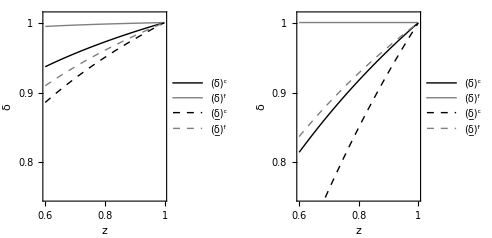

```mathematica
{μ1,σ1,θ1,γ1,ψ1}={.99,2.5,5,1.00001,1};
imagesize=246;
p2bbw=Plot[{
δuc[z,μ1,σ1,θ1,γ1,ψ1],
δuf[z,μ1,σ1,θ1,γ1,ψ1],
δdc[z,μ1,σ1,θ1,γ1,ψ1],
δdf[z,μ1,σ1,θ1,γ1,ψ1]},
{z,0.6,.999},
 PlotStyle->{{AbsoluteThickness[Large],Black},{AbsoluteThickness[Tiny],Gray},{AbsoluteThickness[Large],Dashed,Black},{AbsoluteThickness[Tiny],Dashed,Gray}},
PlotRange->{0.75,1.01},
Frame->True,
RotateLabel->False,
FrameLabel->{{"δ",""},{"z",""}},
PlotLegends->Placed[{"(δ̄)^c","(δ̄)^f","(δ̲)^c","(δ̲)^f"},{.83,.34}],
FrameTicks->{{{.8,.9,1},None},{{.6,.7,.8,.9,1},None}},
ImageSize->0.95*imagesize];

{μ1,σ1,θ1,γ1,ψ1}={.99,1.5,5,1.00001,1};
p3bbw=Plot[{
δuc[z,μ1,σ1,θ1,γ1,ψ1],
δuf[z,μ1,σ1,θ1,γ1,ψ1],
δdc[z,μ1,σ1,θ1,γ1,ψ1],
δdf[z,μ1,σ1,θ1,γ1,ψ1]},
{z,0.6,.999},
 PlotStyle->{{AbsoluteThickness[Large],Black},{AbsoluteThickness[Tiny],Gray},{AbsoluteThickness[Large],Dashed,Black},{AbsoluteThickness[Tiny],Dashed,Gray}},
PlotRange->{0.75,1.01},
Frame->True,
RotateLabel->False,
FrameLabel->{{"δ",""},{"z",""}},
PlotLegends->Placed[{"(δ̄)^c","(δ̄)^f","(δ̲)^c","(δ̲)^f"},{.83,.34}],
FrameTicks->{{{.8,.9,1},None},{{.6,.7,.8,.9,1},None}},
ImageSize->0.95*imagesize];

p32bbw=GraphicsGrid[{{p3bbw, p2bbw}}, ImageSize->imagesize*2]
```

# First best transfers in flexible exchange rate system

We here compute the first best transfers under  flexible exchange rate system.
We define the levels and expectation of utility for a specific transfer T.

```mathematica
UGFBf[z1_,TB_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{ϵGTB,WfT},
ϵGTB=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵGTB,TB];
UGf[z1,ϵGTB,TB,WfT]/.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];
UBFBf[z1_,TB_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{ϵGTB,WfT},
ϵGTB=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵGTB,TB];
UBf[z1,ϵGTB,TB,WfT]/.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];
Welfaref[z1_,TB_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{ϵGTB,WfT},
ϵGTB=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵGTB,TB];
1/2 UGf[z1,ϵGTB,TB,WfT]+1/2 UBf[z1,ϵGTB,TB,WfT]/.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];
TFirstBestf[z_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=(* fast but can miss global maximum *)
FindMaximum[Welfaref[z,T,μ1,σ1,θ1,γ1,ψ1],{T,0.01,-.9,.99}];
```

We compute the critical discount factors that sustain first best.

```mathematica
VGsfFB[z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{TBFB,ϵ00,ϵGTB,Wf0,WfoT,ΔUGf,ΔUBf},
TBFB=T/.TFirstBestf[z,μ1,σ1,θ1,γ1,ψ1][[2]];
ϵ00=ϵ0[z,σ1];
Wf0=Wf[z,ϵ00,0];
ϵGTB=ϵRootGTB[z,TBFB,σ1];
WfoT=Wf[z,ϵGTB,TBFB];
ΔUGf=UGf[z,ϵGTB,TBFB,WfoT]-UGf[z,ϵ00,0,Wf0];
ΔUBf=UBf[z,ϵGTB,TBFB,WfoT]-UBf[z,ϵ00,0,Wf0];
UGf[z,ϵ00,0,Wf0]-UGf[z,ϵ00,0,WfoT]+1/(1-δ)((1-δ/2)ΔUGf+(δ/2)ΔUBf) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

δufFB[z_,μ_,σ_,θ_,γ_,ψ_]:=δ/.FindRoot[VGsfFB[z,δ,μ,σ,θ,γ,ψ]==0,{δ,.5,.999}] //Chop;
```

# Constrained Transfers

We here compute the sustained equilibrium with constrained transfers. 
Constrained transfers are the consumption sharing transfers if V_G  is positive.
If not, they are set so that the value function V_G  is  zero.

## Currency area and constrained transfers

The function VGTBc gives the value function V_G  as a function of transfer TB.
The function TBCc gives the transfer where V_G  is  zero.
The function EUCc gives the expected utility for the constrained transfer. 
We also define functions for the expected consumption, the wage and transfer.

```mathematica
VGTBc[TB_,z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{Wc0,WcoT,ΔUGc,ΔUBc},
Wc0=Wc[z,0];
WcoT=Wc[z,TB];
ΔUGc=UGc[z,TB,WcoT]-UGc[z,0,Wc0];
ΔUBc=UBc[z,TB,WcoT]-UBc[z,0,Wc0];
UGc[z,0,Wc0]-UGc[z,0,WcoT]+1/(1-δ)((1-δ/2)ΔUGc+(δ/2)ΔUBc) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

TBCc[z_,δ_,μ_,σ_,θ_,γ_,ψ_]:=
Module[{},
TB/.FindRoot[VGTBc[TB,z,δ,μ,σ,θ,γ,ψ],{TB,0.999}]// Chop
]

EUCc[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WcT,rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCc[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
WcT=Wc[z1,TB]/.rule;
EUc[z1,TB,WcT]/.rule
]

EXCc[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WcT,rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCc[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
WcT=Wc[z1,TB]/.rule;
(1/2 XGc[z1,TB,WcT]+1/2 XBc[z1,TB,WcT])/.rule
]

TTBCc[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WcT,rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCc[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
TB
]

WCc[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WcT,rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCc[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
WcT=Wc[z1,TB]/.rule;
WcT
]
```

## Flexible exchange rates and constrained transfers

The function VGTBf gives the value function V_G  as a function of transfer TB.
The function TBCf gives the transfer where V_G  is  zero.
The function EUCf gives the expected utility for the constrained transfer. 
We also define functions for the expected consumption, the wage and transfer.

```mathematica
VGTBf[TB_,z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{ϵ00,ϵGTB,Wf0,WfoT,ΔUGf,ΔUBf},
ϵ00=ϵ0[z,σ1];
Wf0=Wf[z,ϵ00,0];
ϵGTB=ϵRootGTB[z,TB,σ1];
WfoT=Wf[z,ϵGTB,TB];
ΔUGf=UGf[z,ϵGTB,TB,WfoT]-UGf[z,ϵ00,0,Wf0];
ΔUBf=UBf[z,ϵGTB,TB,WfoT]-UBf[z,ϵ00,0,Wf0];
UGf[z,ϵ00,0,Wf0]-UGf[z,ϵ00,0,WfoT]+1/(1-δ)((1-δ/2)ΔUGf+(δ/2)ΔUBf) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

TBCf[z_,δ_,μ_,σ_,θ_,γ_,ψ_]:=
Module[{},
TB/.FindRoot[VGTBf[TB,z,δ,μ,σ,θ,γ,ψ],{TB,0.00001,.2}]// Chop (*attention ϵroot function may not find the appropriate root for large TB, so we put lower TB boundary*)
]

EUCf[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WfT,ϵfT, rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCf[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
ϵfT=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵfT,TB]/.rule;
EUf[z1,ϵfT,TB,WfT]/.rule
]

EXCf[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WfT,ϵfT, rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCf[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
ϵfT=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵfT,TB]/.rule;
(1/2 XGf[z1,ϵfT,WfT] +1/2 XBf[z1,ϵfT,WfT])/.rule
]

TTBCf[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WfT,ϵfT, rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCf[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
TB]

WCf[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WfT,ϵfT, rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=Min[TBCf[z1,δ1,μ1,σ1,θ1,γ1,ψ1],TBco[z1]/.rule];
ϵfT=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵfT,TB]/.rule;
WfT
]
```

## Figure 3

We plot the Figure 3 with the expected utility levels in each regime as function of delta. 
There is a range of δ such that currency area is welfare improving.
For large enough δ the expected utility are the same.

```mathematica
{z1,μ1,σ1,θ1,γ1,ψ1}={0.9,0.99,2.,5,5.,1.};
PlotEUCbw=Plot[{Callout[EUCf[z1,δ,μ1,σ1,θ1,γ1,ψ1],Magnify["Flexible",1], {0.875,Below},0.875],Callout[EUCc[z1,δ,μ1,σ1,θ1,γ1,ψ1],Magnify["Currency Area", 1],{0.925,Above},0.925]},{δ,0.8,.999},PlotStyle->{{GrayLevel[0.5],Thick},{GrayLevel[0.2], Thick}},PlotRange->Full];
plot50bw=Show[PlotEUCbw,Frame->True,RotateLabel->False,FrameLabel->{"δ","E_s[U_s^r]"},PlotRange->All, ImageSize->imagesize,FrameTicks->{{None,None},{{0.8,.9,1}, None}}];
```

We now add the expected utility with first best transfers in the flexible exchange rate system. This is displayed  with dashed grey line.

```mathematica
EUCfFB[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,TB1,WfT,ϵfT, rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=T/.Last[TFirstBestf[z1,μ1,σ1,θ1,γ1,ψ1]];
TB1=TBCf[z1,δ1,μ1,σ1,θ1,γ1,ψ1]/.rule;
TB=Min[TB,TB1];
ϵfT=ϵRootGTB[z1,TB,σ1];
ϵfT=ϵRootGTB[z1,TB,σ1];
WfT=Wf[z1,ϵfT,TB]/.rule;
EUf[z1,ϵfT,TB,WfT]/.rule
]

δpoints=Table[δ,{δ,.8,.999,(.999-.8)/80}];
t2= Table[{δ,EUCfFB[z1,δ,μ1,σ1,θ1,γ1,ψ1]},{δ,δpoints}];
PlotEUCFBbw= ListPlot[t2,Joined->True, PlotStyle->{GrayLevel[0.5], Dashed}];
plot60bw=Show[PlotEUCFBbw,Frame->True,PlotRange->All, ImageSize-> imagesize];
```

#### Figure 3

```mathematica
plot5060bw=Show[plot50bw,plot60bw]
```

-Graphics-

## Figure 1

### Display optimal currency areas with constrained transfers

```mathematica
{z1,δ1,μ1,σ1,θ1,γ1,ψ1}={.9,0.95,.99,4,5,1.01,1.0};
ThisPlotPoints=50;
{zmin,zmax,σmin,σmax}={.8,.999,1.1,3.25};

DiffEUcfc[z_,δ_,μ_,σ_,θ_,γ_,ψ_]:=EUCc[z,δ,μ,σ,θ,γ,ψ]-EUCf[z,δ,μ,σ,θ,γ,ψ];
diffEUcEUfc[z_,σ_,γ_] :=DiffEUcfc[z,δ1,μ1,σ,θ1,γ,ψ1];

contplotDiffEUcfc[γ_,hue_]:=ContourPlot[DiffEUcfc[z,δ1,μ1,σ,θ1,γ,ψ1],{z,zmin,zmax},{σ,σmin,σmax},Contours->{10^-15},ContourStyle->GrayLevel[0.5],ContourShading->{None,{Gray,Opacity[.25]}},PlotPoints->ThisPlotPoints]
DistributeDefinitions[contplotDiffEUcfc];
tpl2=ParallelTable[contplotDiffEUcfc[γ,γ/6],{γ,{1.0001,2,3,4,5,6}}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* recompute the fiscal union versus flex *)
contplotEUcEuf[γ_]:=ContourPlot[
diffEUcEUfc[z,σ,γ],{z,zmin,zmax},{σ,σmin,σmax},Contours->{-10^-15},ContourShading->False, PlotPoints->ThisPlotPoints,
ContourStyle->GrayLevel[0.5]];
DistributeDefinitions[contplotEUcEuf];
tpl3=ParallelTable[contplotEUcEuf[γ],{γ,{1.0001,2,3,4,5,6}}];
```

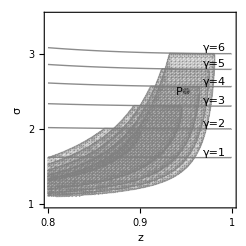

```mathematica
Clear[g1,g2,g3,g4,g5,g6];
g6=Graphics[Text["γ=6",{0.98,3.07}]];
g5=Graphics[Text["γ=5",{0.98,2.86}]];
g4=Graphics[Text["γ=4",{0.98,2.63}]];
g3=Graphics[Text["γ=3",{0.98,2.37}]];
g2=Graphics[Text["γ=2",{0.98,2.07}]];
g1=Graphics[Text["γ=1",{0.98,1.68}]];
p1=Graphics[Text["P",{0.942,2.49}]];
x1=ListPlot[{{0.95,2.5}}, PlotStyle->{PointSize[0.02], Black}, PlotRange->{{0.8,1},{1,3.5}}, AspectRatio->1];
tpl4=Show[Show[x1], Show[TPlot1], Show[tpl2],g6,g5,g4,g3,g2,g1,p1,Frame->True,FrameLabel->{"z","σ"},FrameTicks->{{{1,2,3,4},None},{{.8,.9,1},None}},RotateLabel->False, ImageSize->imagesize]
```

# Sensitivity Analysis - Table 2

The following sensitivity analysis studies the upper and lower bounds of parameter values around the benchmark case provided in the paper. The function FindPositiveRange3 finds the range of parameter where the function F is positive. The function DiffEUcfc returns the difference between expected utility under currency area and flexible exchange rate regime. The analysis reports the range for every parameter of DiffEUcfc. See Table 2 in the text.

```mathematica
DiffEUcfc[z_,δ_,μ_,σ_,θ_,γ_,ψ_]:=EUCc[z,δ,μ,σ,θ,γ,ψ]-EUCf[z,δ,μ,σ,θ,γ,ψ];
FindPositiveRange3[F_,x0_,Minx_,Maxx_,Stepx_]:=Module[{Tup={},Tdown={},FF,xup,xdown},
FF=F[x0]//N//Chop;
If[FF>=0, 
Module[{},
xup=x0;xdown=x0; 
For[x=x0+Stepx,x<=Maxx,x=x+Stepx,
FF=F[x]//N//Chop;
If[FF>=0,AppendTo[Tup,x];xup=x, Break[]]
];
For[x=x0-Stepx,x>=Minx,x=x-Stepx,
FF=F[x]//N//Chop;
If[FF>=0,AppendTo[Tdown,x];xdown=x, Break[]];
];
TT=Union[Tdown//Reverse,Tup];
Return[{xdown,xup}]
],
(*else*)
Print["not positive value for #1=",x0];
Return[{-1,-1}]
];
]
```

```mathematica
{z1,δ1,μ1,σ1,θ1,γ1,ψ1}={0.9,0.95,.99,2,5,5,1}; (* baseline parameters *)
Lz=FindPositiveRange3[DiffEUcfc[#1,δ1,μ1,σ1,θ1,γ1,ψ1]&,z1,.80,.99,.001]; (* Search over z between 0,8 and 0.99 *)
Lδ=FindPositiveRange3[DiffEUcfc[z1,#1,μ1,σ1,θ1,γ1,ψ1]&,δ1,.8,.99,.001];
Lμ=FindPositiveRange3[DiffEUcfc[z1,δ1,#1,σ1,θ1,γ1,ψ1]&,μ1,.2,.99,.01];
Lσ=FindPositiveRange3[DiffEUcfc[z1,δ1,μ1,#1,θ1,γ1,ψ1]&,σ1,1.0001,4.0001,.1];
Lθ=FindPositiveRange3[DiffEUcfc[z1,δ1,μ1,σ1,#1,γ1,ψ1]&,θ1,1.1,10,.1];
Lγ=FindPositiveRange3[DiffEUcfc[z1,δ1,μ1,σ1,θ1,#1,ψ1]&,γ1,1.1,15,.1];
Lψ=FindPositiveRange3[DiffEUcfc[z1,δ1,μ1,σ1,θ1,γ1,#1]&,ψ1,0.00001,10.00001,.01];

tableform1=TableForm[Join[{{δ1,z1,γ1,σ1,θ1,μ1}},Transpose[{Lδ,Lz,Lγ,Lσ, Lθ,Lμ}]],TableHeadings->{{"baseline","min","max"},{"δ", "z","γ","σ","θ", "μ"}}]
(* Note: 10. is the upper bound for "θ" in the search and returned as infinity in the paper *)
```

| δ | z | γ | σ | θ | μ
baseline | 0.95 | 0.9 | 5 | 2 | 5 | 0.99
min | 0.849 | 0.89 | 2.1 | 1.3 | 1.1 | 0.2
max | 0.955 | 0.965 | 6.3 | 2.1 | 10. | 0.99

# Transaction costs

This section studies the effect of money transaction cost. It does not affect the currency area since the latter uses the same currency. It affects the  flexible exchange rate systems where money currency needs to be exchange to pay imports. Let τ be the iceberg exchange rate transaction cost.  All relevant functions are added the argument τ. To avoid confusion with the preceding, a letter τ is added to the function names.
We first make the definitions of the labor supply, price indices ....

```mathematica
LGfτ[z_,ϵ_,TB_,W_]=1/W(1+(TB* ϵ))  ;
LBfτ[z_,ϵ_,TB_,W_]=1/W(1-TB) ;
BGτ[z_,ϵ_,τ_]=(1/2 bG+1/2 τ^(1-σ)ϵ^(1-σ)bB)^(1/(1-σ));
BBτ[z_,ϵ_,τ_]=(1/2 bB+1/2 τ^(1-σ)ϵ^(σ-1)bG)^(1/(1-σ));
PGfτ[z_,ϵ_,W_,τ_]=W A BGτ[z,ϵ,τ] ;
PBfτ[z_,ϵ_,W_,τ_]=W A BBτ[z,ϵ,τ] ;
XGfτ[z_,ϵ_,W_,τ_]=(ξ/μ) (1/PGfτ[z,ϵ,W,τ]);

XBfτ[z_,ϵ_,W_,τ_]=(ξ/μ) (1/PBfτ[z,ϵ,W,τ]);

UGfτ[z_,ϵ_,TB_,W_,τ_]=V[XGfτ[z,ϵ,W,τ]]-(LGfτ[z,ϵ,TB,W])^(1+ψ)/(1+ψ);
UBfτ[z_,ϵ_,TB_,W_,τ_]=V[XBfτ[z,ϵ,W,τ]]-(LBfτ[z,ϵ,TB,W])^(1+ψ)/(1+ψ);
EUfτ[z_,ϵ_,TB_,W_,τ_]=1/2 UGfτ[z,ϵ,TB,W,τ]+1/2 UBfτ[z,ϵ,TB,W,τ];
Wfτ[z_,ϵ_,TB_,τ_]=(κ0 ((1/2(1+TB*ϵ)^(1+ψ)+1/2(1-TB)^(1+ψ))/(A^(γ-1)(1/2(1+TB*ϵ)(BGτ[z,ϵ,τ])^(γ-1)+1/2(1-TB)(BBτ[z,ϵ,τ])^(γ-1)))))^(1/(γ+ψ));
```

```mathematica
ϵ0[z_,σ_]=(bG/bB)^(-1/σ); (* exchange rate at zero transfers and zero transaction costs*)
Υτ[z_,σ_,ϵ_,τ_]=(bG+bB τ^(1-σ)ϵ^(1-σ))/(bB ϵ^(1-σ)+bG τ^(1-σ))// Factor;
```

We write the implicit equation for  Home exchange rate  in good state for a TG<0.
The Home exchange rate  in Good state when transfer is TG <0  is a root of the previous implicit equation.

```mathematica
ExchEQGTGτ[eG_,z_,TG_,σ_,τ_]=eG-(bG/bB)^(-1/σ) ((1-TG)/(1+TG/eG))^(1/σ)((τ^(1-σ)+ϵ Υτ[z,σ,ϵ,τ])/(1+τ^(1-σ)ϵ Υτ[z,σ,ϵ,τ]))^(1/σ) ;
(* this is equivalent to the following definition*)

ExchEQGTGτ[eG_,z_,TG_,σ_,τ_]=eG-(bB/bG(1-TG)/(1+TG/eG)(τ^(1-σ)+eG Υτ[z,σ,eG,τ])/(1+τ^(1-σ)eG Υτ[z,σ,eG,τ]))^(1/σ) ;


ϵRootGTGτ[z_,TG_,σ_,τ_]:= Module[{eG},
eG/.FindRoot[ExchEQGTGτ[eG,z,TG,σ,τ],{eG,ϵ0[z,σ]}]
];
```

Home exchange rate  in Good state when transfer in bad state is TB= -TG/ϵ >0 :  a root of the previous implicit equation.
We prefer this solution.

```mathematica
ExchEQGTBτ[eG_,z_,TB_,σ_,τ_]=eG-(bB/bG(1+eG TB)/(1-TB)(τ^(1-σ)+eG Υτ[z,σ,eG,τ])/(1+τ^(1-σ)eG Υτ[z,σ,eG,τ]))^(1/σ) ;
ϵRootGTBτ[z_,TB_,σ_,τ_]:= Module[{eG}, eG/.FindRoot[ExchEQGTBτ[eG,z,TB,σ,τ],{eG,ϵ0[z,σ]}]]
```

## Comparison between expected utilities in Currency areas and flexible exchange rate regime

We here plot the loci where currency areas with consumption sharing yields the same expected utility as flexible exchange rate with zero transfers.  The function DifferenceEUcfτ computes the difference in expected utility.

```mathematica
DifferenceEUcfτ[z1_,μ1_,σ1_,θ1_,γ1_,ψ1_,τ1_]:=Module[{e1,W1,rule1,TB2,W2},
rule1={μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
e1=ϵRootGTBτ[z1,0,σ1,τ1];
W1=Wfτ[z1,e1,0,τ1]/.rule1;
TB2=TBco[z1]/.rule1;
W2=Wc[z1,TB2]/.rule1;
(EUc[z1,TB2,W2]-EUfτ[z1,e1,0,W1,τ1])/. rule1
];
```

## Consumption sharing under transaction costs

We compute the exchange rate and transfer under consumption sharing and transaction cost.

```mathematica
ϵGfoτ[z_,σ_,τ_]=(1/(2 τ^(1-σ))((1-bG/bB)+√((1-bG/bB)^2+4 τ^(2(1-σ))bG/bB)))^(1/(1-σ));

TGfoτ[z_,σ_,τ_]=((1-bG/bB(ϵG^σ τ^(σ-1)(1+τ^(1-σ)ϵG^σ)/(1+τ^(σ-1)ϵG^σ)))/(1+1/ϵG bG/bB(ϵG^σ τ^(σ-1)(1+τ^(1-σ)ϵG^σ)/(1+τ^(σ-1)ϵG^σ)))/.ϵG->ϵGfoτ[z,σ,τ]);
TBfoτ[z_,σ_,τ_]=-((1-bG/bB(ϵG^σ τ^(σ-1)(1+τ^(1-σ)ϵG^σ)/(1+τ^(σ-1)ϵG^σ)))/(ϵG+bG/bB(ϵG^σ τ^(σ-1)(1+τ^(1-σ)ϵG^σ)/(1+τ^(σ-1)ϵG^σ)))/.ϵG->ϵGfoτ[z,σ,τ]);
```

## Constrained transfers and transaction costs (Figure 4)

```mathematica
ΔVGdfτTB[TB_,z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_,τ1_]:=Module[{ϵ00,ϵGTB,Wf0,WfoT,ΔUGfτ,ΔUBfτ},
ϵ00=ϵRootGTBτ[z,0,σ1,τ1];
Wf0=Wfτ[z,ϵ00,0,τ1];
ϵGTB=ϵRootGTBτ[z,TB,σ1,τ1];
WfoT=Wfτ[z,ϵGTB,TB,τ1];
ΔUGfτ=UGfτ[z,ϵGTB,TB,WfoT,τ1]-UGfτ[z,ϵ00,0,Wf0,τ1];
ΔUBfτ=UBfτ[z,ϵGTB,TB,WfoT,τ1]-UBfτ[z,ϵ00,0,Wf0,τ1];
UGfτ[z,ϵ00,0,Wf0,τ1]-UGfτ[z,ϵ00,0,WfoT,τ1]+1/(1-δ)((1-δ/2)ΔUGfτ+(δ/2)ΔUBfτ) /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];

EUfτconstr[z2_,δ2_,μ2_,σ2_,θ2_,γ2_,ψ2_,τ2_]:=Module[{},
r3={z->z2,δ->δ2,μ->μ2,σ->σ2,θ->θ2,γ->γ2,ψ->ψ2,τ->τ2};
fct[TB3_?NumericQ]:=ΔVGdfτTB[TB3,z2,δ2,μ2,σ2,θ2,γ2,ψ2,τ2];
TBshare3=TBfoτ[z2,σ2,τ2];
TBconstr3=TB/.FindRoot[fct[TB],{TB,TBshare3}];
TB3=Max[0,Min[TBshare3,TBconstr3]];
ϵ3=ϵRootGTBτ[z2,TB3,σ2,τ2];
W3=Wfτ[z2,ϵ3,TB3,τ2] /.r3;
EUfτ[z2,ϵ3,TB3,W3,τ2] /.r3
]

DiffEUcfcτ[z_,δ_,μ_,σ_,θ_,γ_,ψ_,τ_]:=EUCc[z,δ,μ,σ,θ,γ,ψ]-EUfτconstr[z,δ,μ,σ,θ,γ,ψ,τ];
```

```mathematica
{δ2,γ2,ψ2,μ2,θ2}={.95,1.01,1,.99,5};
{zmin,zmax,σmin,σmax}={.6,.999,1.01,6};
ThisPlotPoints=5;

contplotDiffEUcfcτ[τ_]:=
ContourPlot[DiffEUcfcτ[z,δ2,μ2,σ,θ2,γ2,ψ2,τ],{z,zmin,zmax},{σ,σmin,σmax},Contours->{0.00000000001}, ContourStyle->GrayLevel[0.1],ContourShading->{None,{Gray,Opacity[.25]}},PlotPoints->ThisPlotPoints];
```

```mathematica
t0=Graphics[Text["τ=1.000",{0.88,1.92}]];
t01=Graphics[Text["τ=1.001",{0.90,2.20}]];
t05=Graphics[Text["τ=1.005",{0.913,2.90}]];
t10=Graphics[Text["τ=1.010",{0.909,3.33}]];
t15=Graphics[Text["τ=1.015",{0.917,3.89}]];
```

```mathematica
ThisPlotPoints=30;
{δ2,γ2,ψ2,μ2,θ2}={.95,2,1,.99,5};
listτ={1,1.001,1.005,1.01,1.015};
lplots=ParallelTable[
ContourPlot[DiffEUcfcτ[z,δ2,μ2,σ,θ2,2,ψ2,τ],{z,.8,zmax},{σ,1.01,4},Contours->{0.00000000001}, ContourStyle->GrayLevel[0.7],ContourShading->{None,{Gray,Opacity[.25]}},PlotPoints->ThisPlotPoints]//Quiet,
{τ,listτ}];
```

```mathematica
TPlot2=Show[
ParallelTable[
ContourPlot[
DifferenceEUcfτ[z,μ2,σ,θ2,γ2,ψ2,τ],{z,.8,.999},{σ,1.01,4},Contours->{0},ContourShading->False, PlotPoints->Floor[ThisPlotPoints *2],
 ContourStyle->GrayLevel[0.1]
],
{τ,listτ}]
];
```

### Here is Figure 4.

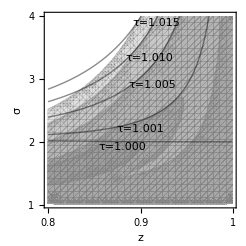

```mathematica
plot450=Show[lplots,TPlot2,t0,t01,t05,t10,t15,FrameLabel->{"z","σ"},FrameTicks->{{{1,2,3,4},None},{{.8,.9,1},None}},RotateLabel->False, ImageSize->imagesize]
```

# Secede and Return to Flexible Exchange Rate (Table 4)

Another way to compute the constrained optimum for currency area

## Currency area and constrained transfers with return to flexible exchange rates: delayed secession

The function VGTBc gives the value function V_G  as a function of transfer TB.
The function TBCc gives the transfer where V_G  is  zero.
The function EUCc gives the expected utility for the constrained transfer. 
We also define functions for the expected consumption, the wage and transfer. 

At the period of secession, the seceding country sets a zero transfer but remains in the currency area for the whole period.
Then, it is under flexible exchange rate regime in the periods after secession.

```mathematica
VGTBcReturn[TB_,z_,δ_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=
Module[{UGcT,UBcT,UGc0,WcT,ϵ00,Wf0,UGf0,UBf0},

WcT=Wc[z,TB];
UGcT=UGc[z,TB,WcT];
UBcT=UBc[z,TB,WcT];
UGc0=UGc[z,0,WcT];(*delayed secession *)

ϵ00=ϵ0[z,σ1];
Wf0=Wf[z,ϵ00,0];
UGf0=UGf[z,ϵ00,0,Wf0];
UBf0=UBf[z,ϵ00,0,Wf0];

(1+1/2 δ/(1-δ))UGcT+(1/2 δ/(1-δ))UBcT-UGc0-(1/2 δ/(1-δ))UGf0-(1/2 δ/(1-δ))UBf0 /.{μ-> μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1}//N
];


TBCcReturn[z_,δ_,μ_,σ1_,θ_,γ_,ψ_]:=
Module[{TBmax,rr,TBmax2},
(* it is assumed that VGTBcReturn[0,z,δ,μ,σ1,θ,γ,ψ]<0,*)
TBmax=TBco[z]/.σ->σ1; (*use the optimal transfer as starting point*)
If[VGTBcReturn[TBmax,z,δ,μ,σ1,θ,γ,ψ]>0,
(*then optimal transfer is sustained *)
Return[TBmax]];
(* otherwise there is a constrained transfer  on the interval 0 to TBmax*)
rr=FindMaximum[{VGTBcReturn[TB,z,δ,μ,σ1,θ,γ,ψ],0≤TB},{TB,TBmax}];
If[rr[[1]]<0,Return[0]]; (*in this case, no positive values*)
(*otherwise find root between TB=0 and the argument of the max of VGTBcReturn*)
TBmax2=TB/.rr[[2,1]];
TB/.FindRoot[VGTBcReturn[TB,z,δ,μ,σ1,θ,γ,ψ],{TB,TBmax2,TBmax}]// Chop
]
EUCcReturn[z1_,δ1_,μ1_,σ1_,θ1_,γ1_,ψ1_]:=Module[{TB,WcT,rule},
rule={z->z1,δ->δ1,μ->μ1,σ->σ1,θ->θ1,γ->γ1,ψ->ψ1};
TB=TBCcReturn[z1,δ1,μ1,σ1,θ1,γ1,ψ1];
WcT=Wc[z1,TB]/.rule;
EUc[z1,TB,WcT]/.rule
];
```

```mathematica
{z1,δ1,μ1,σ1,θ1,γ1,ψ1}={0.85,0.95,.99,1.25,5,9,1};
DiffEUcfcReturn[z_,δ_,μ_,σ_,θ_,γ_,ψ_]:=EUCcReturn[z,δ,μ,σ,θ,γ,ψ]-EUCf[z,δ,μ,σ,θ,γ,ψ];
```

Here is Table 4

```mathematica
Print["The difference in welfare should be positive: DiffEUcfcReturn=",DiffEUcfcReturn[z1,δ1,μ1,σ1,θ1,γ1,ψ1] ];

Lz=FindPositiveRange3[DiffEUcfcReturn[#1,δ1,μ1,σ1,θ1,γ1,ψ1]&,z1,.80,.99,.001];
Lδ=FindPositiveRange3[DiffEUcfcReturn[z1,#1,μ1,σ1,θ1,γ1,ψ1]&,δ1,.8,.99,.001];
Lσ=FindPositiveRange3[DiffEUcfcReturn[z1,δ1,μ1,#1,θ1,γ1,ψ1]&,σ1,1.0001,2.0001,.01];
Lθ=FindPositiveRange3[DiffEUcfcReturn[z1,δ1,μ1,σ1,#1,γ1,ψ1]&,θ1,1.1,10,.1];
Lγ=FindPositiveRange3[DiffEUcfcReturn[z1,δ1,μ1,σ1,θ1,#1,ψ1]&,γ1,1.1,18,.1];
Lμ=FindPositiveRange3[DiffEUcfc[z1,δ1,#1,σ1,θ1,γ1,ψ1]&,μ1,.25,.99,.01];



tt=TableForm[Join[{{δ1,z1,γ1,σ1,θ1,μ1}},Transpose[{Lδ,Lz,Lγ,Lσ, Lθ,Lμ}]],TableHeadings->{{"baseline","min","max"},{"δ","z", "γ","σ","θ","μ"}}]
```

The difference in welfare should be positive: DiffEUcfcReturn=2.59305×10^-6

| δ | z | γ | σ | θ | μ
baseline | 0.95 | 0.85 | 9 | 1.25 | 5 | 0.99
min | 0.939 | 0.81 | 7.5 | 1.18 | 2.7 | 0.25
max | 0.961 | 0.874 | 12.6 | 1.35 | 10. | 0.99